```mathematica
(*Import packages*)
$LoadFeynArts = True;
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path,FileNameJoin[{NotebookDirectory[],"include"}]];
<< XSec`
<< TreeLevel`
<< CalcTools`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

CT::shdw: Symbol CT appears in multiple contexts {CalcTools`,Global`}; definitions in context CalcTools` may shadow or be shadowed by other definitions.

## Square amplitudes

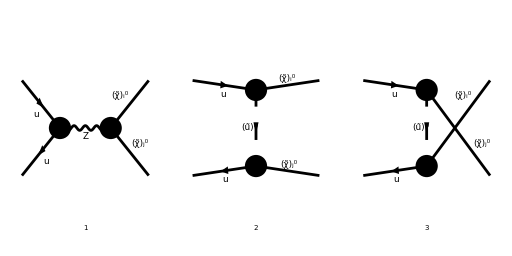

```mathematica
treeDiagrams = InsertFields[
CreateTopologies[0, 2->2,ExcludeTopologies->{Boxes,SelfEnergies,Tadpoles}], 
{F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD,
Restrictions->{NoLightFHCoupling,NoElectronHCoupling},
ExcludeParticles->{F[11],F[12],S[1],S[2],S[3],S[4]}
];
Paint[treeDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

```mathematica
Subscript[M, 0][0]=FCFAConvert[
CreateFeynAmp[treeDiagrams], 
IncomingMomenta->{ki,kj}, OutgoingMomenta->{pi,pj},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
SMP->True,
DropSumOver->True,
LorentzIndexNames->{μ,ν}
]/.AmpSimplifyRules/.{IndexDelta->FeynCalc`IndexDelta};
```

```mathematica
temp=SMP["g_W"]^2 FeynCalc`IndexDelta[a,b];
```

```mathematica
Subscript[M, 0][1]=temp*DiracSimplify/@(Convert2QZCharges/@(Subscript[M, 0][0]/temp));
Subscript[M, 0][2]=Subscript[M, 0][1]/.{Opp[i_,j_,L]*->-Opp[i,j,R]}//.SuperChargeRules;
```

```mathematica
MakeBoxes[DSf[s_,t_,g_],TraditionalForm]:=SubscriptBox["Δ",MakeBoxes[s,TraditionalForm]]
MakeBoxes[DSfC[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"*"]
MakeBoxes[DZ,TraditionalForm]=SubscriptBox["Δ","Z"];
MakeBoxes[FeynCalc`Index[Sfermion,a_],TraditionalForm]:=MakeBoxes[a,TraditionalForm]

MakeBoxes[Den[p2_,m2_],TraditionalForm]:=MakeBoxes[1/(p2-m2),TraditionalForm]
MakeBoxes[tMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"t"]
MakeBoxes[uMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"u"]
```

```mathematica
(*Subscript[M, s][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],1]]/.SMP["m_Z"]^2->DZ;
Subscript[M, t][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],2]]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];
Subscript[M, u][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],3]]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];*)
Subscript[M, s][0]=(Part[Subscript[M, 0][0],1]/.ZSimplifyRules//FeynAmpDenominatorExplicit)/.SMP["m_Z"]^2->DZ;
Subscript[M, t][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][0],2]//Convert2QZCharges]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];
Subscript[M, u][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][0],3]//Convert2QZCharges]/.{SMP["m_Z"]^2->DZ,MSf[a_,t_,g_]^2->DSf[a,t,g]}/.Index[Sfermion,5]->Index[Sfermion,A];
```

```mathematica
Subscript[M̄, s][0]=ConjugateAmplitude[Subscript[M, s][0]]/.{A->B,μ->ρ,ν->σ};
Subscript[M̄, t][0]=ConjugateAmplitude[Subscript[M, t][0]]/.{A->B,μ->ρ,ν->σ};
Subscript[M̄, u][0]=ConjugateAmplitude[Subscript[M, u][0]]/.{A->B,μ->ρ,ν->σ};
```

```mathematica
(*Square the amplitudes*)
Subscript[I, ss][0]=SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, s][0]];
Subscript[I, tt][0]=SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, t][0]];
Subscript[I, uu][0]=SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, u][0]];
Subscript[I, st][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, t][0]/.B->A]+SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, s][0]])/2;
Subscript[I, su][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, u][0]/.B->A]+SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, s][0]])/2;
Subscript[I, tu][0]=(SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, u][0]]+SquareAmplitudes[Subscript[M, u][0]/.A->B,Subscript[M̄, t][0]/.B->A])/2;
```

```mathematica
Subscript[I, ss][1]=FixDimension[Subscript[I, ss][0]/.Convert2Den];
Subscript[I, tt][1]=FixDimension[Subscript[I, tt][0]/.Convert2Den];
Subscript[I, uu][1]=FixDimension[Subscript[I, uu][0]/.Convert2Den];
Subscript[I, st][1]=FixDimension[Subscript[I, st][0]/.Convert2Den];
Subscript[I, su][1]=FixDimension[Subscript[I, su][0]/.Convert2Den];
Subscript[I, tu][1]=FixDimension[Subscript[I, tu][0]/.Convert2Den];
```

```mathematica
(*Common prefactor for the squared amplitudes.*)
Prefactor=4 (FeynCalc`IndexDelta[a,b])^2 SMP["g_W"]^4;
Subscript[I, ss][2]=Prefactor FactorDenominators[Subscript[I, ss][1]/Prefactor];
Subscript[I, tt][2]=Prefactor FactorDenominators[Subscript[I, tt][1]/Prefactor];
Subscript[I, uu][2]=Prefactor FactorDenominators[Subscript[I, uu][1]/Prefactor];
Subscript[I, st][2]=Prefactor FactorDenominators[Subscript[I, st][1]/Prefactor];
Subscript[I, su][2]=Prefactor FactorDenominators[Subscript[I, su][1]/Prefactor];
Subscript[I, tu][2]=Prefactor FactorDenominators[Subscript[I, tu][1]/Prefactor];
```

```mathematica
Prefactor Collect[
Expand[Subscript[I, ss][2]/Prefactor]/.{Opp[args__,L]*->-Opp[args,R],Opp[args__,R]*->-Opp[args,L]}//.SuperChargeRules,
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
FullSimplify
]
```

4 g_W^4 δ_ab^2 (1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2) (-m_i^2 (-2 m_j^2+t+u)-m_j^2 (t+u)+t^2+u^2)-s m_i m_j 1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2))

```mathematica
(*Add squared amplitudes together, omitting prefactor and change to supercharges.*)
Itot[0]=(Subscript[I, ss][2]+Subscript[I, tt][2]+Subscript[I, uu][2]+2 Subscript[I, st][2]+2 Subscript[I, su][2]+2 Subscript[I, tu][2])/Prefactor;
Itot[1]=Collect[
Itot[0],
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
(Collect[
#1,
Den[args1__]Den[args2__],
(FullSimplify[Expand[#1]/.{Opp[args__,L]*->-Opp[args,R],Opp[args__,R]*->-Opp[args,L]}//.SuperChargeRules]&)
]&)
]
```

(t-m_i^2) (t-m_j^2) (1/(t-Δ_SfeA) 1/(t-Δ_SfeB^*) (Q_SfeB^(L R̄) Conjugate[(Q_SfeA^(L R̄))]+Q_SfeB^(R L̄) Conjugate[(Q_SfeA^(R L̄))]+Q_SfeB^(L L̄) Conjugate[(Q_SfeA^(L L̄))]+Q_SfeB^(R R̄) Conjugate[(Q_SfeA^(R R̄))])+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA) (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Conjugate[(Q_SfeA^(R R̄))])+1/(s-Δ_Z) 1/(t-Δ_SfeA^*) (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+(u-m_i^2) (u-m_j^2) (1/(u-Δ_SfeA) 1/(u-Δ_SfeB^*) (Q_SfeA^(L R̄) Conjugate[(Q_SfeB^(L R̄))]+Q_SfeA^(R L̄) Conjugate[(Q_SfeB^(R L̄))]+Q_SfeA^(L L̄) Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Q_SfeB^(R R̄))])+1/(s-Conjugate[(Δ_Z)]) 1/(u-Δ_SfeA) (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])+1/(s-Δ_Z) 1/(u-Δ_SfeA^*) (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Conjugate[(Q_SfeA^(R R̄))])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+s m_i m_j (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]-Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))])+(-Q_SfeA^(L L̄) Q_SfeB^(L L̄)-Q_SfeA^(R R̄) Q_SfeB^(R R̄)) 1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB)+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA) (Conjugate[(Z_s^L)] (-Conjugate[(Q_SfeA^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))])+1/(s-Δ_Z) 1/(u-Δ_SfeA^*) (Conjugate[(Z_s^L)] (-Conjugate[(Q_SfeA^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))])+1/(s-Conjugate[(Δ_Z)]) 1/(u-Δ_SfeA) (Z_s^L (-Q_SfeA^(L L̄))-Z_s^R Q_SfeA^(R R̄))+1/(s-Δ_Z) 1/(t-Δ_SfeA^*) (Z_s^L (-Q_SfeA^(L L̄))-Z_s^R Q_SfeA^(R R̄))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2))+(t u-m_i^2 m_j^2) (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))])+(Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)) 1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB))

```mathematica
(*Show that the total amplitude can be written as effective charges in front of these four kinematic terms.*)
Collect[
Itot[1],
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
(Isolate[#1//Simplify,IsolateNames->Q]&)
]
```

Q(1674) s m_i m_j+Q(1684) (t u-m_i^2 m_j^2)+Q(1679) (t-m_i^2) (t-m_j^2)+Q(1681) (u-m_i^2) (u-m_j^2)

```mathematica
DifferentialCrossSection=Prefactor/(64 Subscript[N, C]^2 π s^2)Itot[1]/.{(FeynCalc`IndexDelta[a,b])^p_->Subscript[N, C],SMP["g_W"]->Sqrt[4π Subscript[α, W]]}
```

1/(s^2 N_C)π α_W^2 ((t-m_i^2) (t-m_j^2) (1/(t-Δ_SfeA) 1/(t-Δ_SfeB^*) (Q_SfeB^(L R̄) Conjugate[(Q_SfeA^(L R̄))]+Q_SfeB^(R L̄) Conjugate[(Q_SfeA^(R L̄))]+Q_SfeB^(L L̄) Conjugate[(Q_SfeA^(L L̄))]+Q_SfeB^(R R̄) Conjugate[(Q_SfeA^(R R̄))])+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA) (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Conjugate[(Q_SfeA^(R R̄))])+1/(s-Δ_Z) 1/(t-Δ_SfeA^*) (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+(u-m_i^2) (u-m_j^2) (1/(u-Δ_SfeA) 1/(u-Δ_SfeB^*) (Q_SfeA^(L R̄) Conjugate[(Q_SfeB^(L R̄))]+Q_SfeA^(R L̄) Conjugate[(Q_SfeB^(R L̄))]+Q_SfeA^(L L̄) Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Q_SfeB^(R R̄))])+1/(s-Conjugate[(Δ_Z)]) 1/(u-Δ_SfeA) (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])+1/(s-Δ_Z) 1/(u-Δ_SfeA^*) (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Conjugate[(Q_SfeA^(R R̄))])+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))+s m_i m_j (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]-Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))])+(-Q_SfeA^(L L̄) Q_SfeB^(L L̄)-Q_SfeA^(R R̄) Q_SfeB^(R R̄)) 1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB)+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA) (Conjugate[(Z_s^L)] (-Conjugate[(Q_SfeA^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))])+1/(s-Δ_Z) 1/(u-Δ_SfeA^*) (Conjugate[(Z_s^L)] (-Conjugate[(Q_SfeA^(L L̄))])-Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))])+1/(s-Conjugate[(Δ_Z)]) 1/(u-Δ_SfeA) (Z_s^L (-Q_SfeA^(L L̄))-Z_s^R Q_SfeA^(R R̄))+1/(s-Δ_Z) 1/(t-Δ_SfeA^*) (Z_s^L (-Q_SfeA^(L L̄))-Z_s^R Q_SfeA^(R R̄))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2))+(t u-m_i^2 m_j^2) (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))])+(Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)) 1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB)))

## Integrate over t

```mathematica
(*To simplify before integrating over t, we will need to convert all terms containing u to t.*)
Itot[2]=Collect[
Itot[1]/.{Den[u,DSf[args__]]->-Den[t,uMass[args]],Den[u,DSfC[args__]]->-Den[t,uMass[args]*],Den[t,DSf[args__]]->Den[t,tMass[args]],Den[t,DSfC[args__]]->Den[t,tMass[args]*]}/.{u->MNeu[i]^2+MNeu[j]^2-s-t}//Expand,
Den[args1__]Den[args2__],
Simplify
]
```

1/(t-Conjugate[(Δ_SfeB^u)]) 1/(t-Δ_SfeA^t) (s (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]) m_i m_j+Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))] ((m_j^2-t) m_i^2+t (-m_j^2+s+t))+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))] ((m_j^2-t) m_i^2+t (-m_j^2+s+t)))+1/(t-Conjugate[(Δ_SfeB^u)]) 1/(t-Δ_SfeA^u) (-m_i^2+s+t) (-m_j^2+s+t) (Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄))+1/(t-Conjugate[(Δ_SfeB^t)]) 1/(t-Δ_SfeA^t) (t-m_i^2) (t-m_j^2) (Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)+Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄))+1/(t-Conjugate[(Δ_SfeA^t)]) 1/(t-Δ_SfeB^u) (-((t-m_j^2) (Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)) m_i^2)+s m_j (Q_SfeA^(L L̄) Q_SfeB^(L L̄)+Q_SfeA^(R R̄) Q_SfeB^(R R̄)) m_i+t (-m_j^2+s+t) (Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)))+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA^t) (-Conjugate[(Q_SfeA^(L L̄))] (s Conjugate[(Z_s^L)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^L)-Conjugate[(Q_SfeA^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^R))+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_SfeA^u)]) (Conjugate[(Q_SfeA^(L L̄))] (s Conjugate[(Z_s^L)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^L)+Conjugate[(Q_SfeA^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^R))+1/(s-Δ_Z) 1/(t-Conjugate[(Δ_SfeA^t)]) (Conjugate[(Z_s^L)] (t-m_i^2) (t-m_j^2) Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] (t-m_i^2) (t-m_j^2) Q_SfeA^(R R̄)-s m_i m_j (Q_SfeA^(L L̄) Z_s^L+Q_SfeA^(R R̄) Z_s^R))+1/(s-Conjugate[(Δ_Z)]) 1/(t-Δ_SfeA^u) (-Conjugate[(Z_s^L)] (-m_i^2+s+t) (-m_j^2+s+t) Q_SfeA^(L L̄)-Conjugate[(Z_s^R)] (-m_i^2+s+t) (-m_j^2+s+t) Q_SfeA^(R R̄)+s m_i m_j (Q_SfeA^(L L̄) Z_s^L+Q_SfeA^(R R̄) Z_s^R))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) (-s m_i m_j (Conjugate[(Z_s^L)])^2+(s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t)) Z_s^L Conjugate[(Z_s^L)]-s (Conjugate[(Z_s^R)])^2 m_i m_j+Conjugate[(Z_s^R)] (s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t)) Z_s^R-s m_i m_j ((Z_s^L)^2+(Z_s^R)^2))

```mathematica
(*Convert all t-dependence to a dictionary of standard t-integrals Subscript[T, d]^p(Subscript[Δ, 1],...,Subscript[Δ, d]).*)
ItotIntegrals[0]=ToTIntegrals[Itot[2]]
ItotIntegrals[1]=ReduceTIntegrals[ItotIntegrals[0]]
```

CT(1471) T_2^0(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])-CT(1479) T_2^1(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+CT(1470) T_2^2(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+CT(1469) T_2^0(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(1474) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(1478) T_2^1(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(1480) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(1467) T_2^2(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(1472) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(1476) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(1481) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(1475) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(1448) T_1^0(Conjugate[(Δ_SfeA^t)])-CT(1462) T_1^1(Conjugate[(Δ_SfeA^t)])+CT(1465) T_1^2(Conjugate[(Δ_SfeA^t)])+CT(1453) T_1^0(Conjugate[(Δ_SfeA^u)])-CT(1486) T_1^1(Conjugate[(Δ_SfeA^u)])-CT(1488) T_1^2(Conjugate[(Δ_SfeA^u)])+CT(1457) T_1^0(Δ_SfeA^t)-CT(1487) T_1^1(Δ_SfeA^t)+CT(1489) T_1^2(Δ_SfeA^t)+CT(1459) T_1^0(Δ_SfeA^u)-CT(1464) T_1^1(Δ_SfeA^u)-CT(1466) T_1^2(Δ_SfeA^u)+CT(1445) T_0^0+2 CT(1483) T_0^1+2 CT(1484) T_0^2

CT(1500) T_1^0(Conjugate[(Δ_SfeA^t)])+CT(1505) T_1^0(Conjugate[(Δ_SfeA^u)])+CT(1518) T_1^0(Δ_SfeA^t)+CT(1512) T_1^0(Δ_SfeA^u)+CT(1503) T_1^0(Conjugate[(Δ_SfeB^t)])+CT(1508) T_1^0(Conjugate[(Δ_SfeB^u)])+CT(1490) T_0^0+CT(1496) T_0^1+2 CT(1484) T_0^2

```mathematica
(*We can write it out in terms of the basic charges using GetKinematicCoefficients.*)
Collect[ItotIntegrals[0],tIntegral[args__],GetKinematicCoefficients]
```

m_i^2 (Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)+Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) T_2^0(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)]) m_j^2+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) ((-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_i^2+(-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_j^2+s (2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2)) T_0^1+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) 1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) T_0^2+1/(s-Δ_Z) ((-Conjugate[(Z_s^L)] Q_SfeA^(L L̄)-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Z_s^L)] Q_SfeA^(L L̄)-Conjugate[(Z_s^R)] Q_SfeA^(R R̄))) T_1^1(Conjugate[(Δ_SfeA^t)])+1/(s-Conjugate[(Δ_Z)]) ((Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_i^2+s (-2 Conjugate[(Z_s^L)] Q_SfeA^(L L̄)-2 Conjugate[(Z_s^R)] Q_SfeA^(R R̄))+m_j^2 (Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄))) T_1^1(Δ_SfeA^u)+1/(s-Δ_Z) (Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) T_1^2(Conjugate[(Δ_SfeA^t)])+1/(s-Conjugate[(Δ_Z)]) (-Conjugate[(Z_s^L)] Q_SfeA^(L L̄)-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) T_1^2(Δ_SfeA^u)+(m_i^2 (Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)) m_j^2+s m_i (Q_SfeA^(L L̄) Q_SfeB^(L L̄)+Q_SfeA^(R R̄) Q_SfeB^(R R̄)) m_j) T_2^0(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+((Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))]) m_i^2 m_j^2+s (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]) m_i m_j) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+((Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)) s^2+m_i^2 (-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)-Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)) s+m_j^2 (-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)-Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)) s+m_i^2 m_j^2 (Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄))) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+((-Q_SfeA^(R L̄) Q_SfeB^(L R̄)-Q_SfeA^(L R̄) Q_SfeB^(R L̄)) m_i^2+m_j^2 (-Q_SfeA^(R L̄) Q_SfeB^(L R̄)-Q_SfeA^(L R̄) Q_SfeB^(R L̄))+s (Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄))) T_2^1(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+((-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)-Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)-Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)-Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)-Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)-Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)-Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄))) T_2^1(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+((-Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]-Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))]) m_i^2+(-Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]-Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))]) m_j^2+s (Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))])) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+((-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)-Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)-Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄))+s (2 Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+2 Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+2 Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+2 Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄))) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+(Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)) T_2^2(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+(Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)+Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) T_2^2(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+(Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))]) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+(Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+1/(s-Δ_Z) T_1^2(Conjugate[(Δ_SfeA^u)]) (-Conjugate[(Q_SfeA^(L L̄))] Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+1/(s-Conjugate[(Δ_Z)]) T_1^2(Δ_SfeA^t) (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+1/(s-Conjugate[(Δ_Z)]) T_1^1(Δ_SfeA^t) ((-Conjugate[(Q_SfeA^(L L̄))] Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_i^2+m_j^2 (-Conjugate[(Q_SfeA^(L L̄))] Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R))+1/(s-Δ_Z) T_1^1(Conjugate[(Δ_SfeA^u)]) ((Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_i^2+s (-2 Conjugate[(Q_SfeA^(L L̄))] Z_s^L-2 Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+m_j^2 (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))+1/(s-Δ_Z) T_1^0(Conjugate[(Δ_SfeA^u)]) ((-Conjugate[(Q_SfeA^(L L̄))] Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s^2+(Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j s+m_i^2 (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s+m_j^2 (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s+m_i^2 m_j^2 (-Conjugate[(Q_SfeA^(L L̄))] Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R))+1/(s-Conjugate[(Δ_Z)]) T_1^0(Δ_SfeA^t) (m_i^2 (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_j^2+s (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j)+1/(s-Δ_Z) T_1^0(Conjugate[(Δ_SfeA^t)]) (m_i^2 (Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_j^2+s m_i (-Q_SfeA^(L L̄) Z_s^L-Q_SfeA^(R R̄) Z_s^R) m_j)+1/(s-Conjugate[(Δ_Z)]) T_1^0(Δ_SfeA^u) ((-Conjugate[(Z_s^L)] Q_SfeA^(L L̄)-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s^2+m_i^2 (Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s+m_j^2 (Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s+m_i m_j (Q_SfeA^(L L̄) Z_s^L+Q_SfeA^(R R̄) Z_s^R) s+m_i^2 m_j^2 (-Conjugate[(Z_s^L)] Q_SfeA^(L L̄)-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)))+1/(s-Δ_Z) 1/(s-Conjugate[(Δ_Z)]) T_0^0 ((Abs[Z_s^L]^2+Abs[Z_s^R]^2) s^2+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_i^2 s+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_j^2 s+m_i m_j (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2) s+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) m_i^2 m_j^2)

```mathematica
(*A function for collecting all effective charges in an expression.*)
EffectiveCharges={
Qtu[args1__]Qtu[args2__],
Qtu[args1__]Qtu[args2__]*,
Qtu[args1__]*Qtu[args2__]*,
QtuC[args1__]QtuC[args2__],
QtuC[args1__]QtuC[args2__]*,
QtuC[args1__]*QtuC[args2__]*,
Zs[arg_]QtuC[args__],
Zs[arg_]*QtuC[args__],
Zs[arg_]QtuC[args__]*,
Zs[arg_]*QtuC[args__]*
};
CollectEffCharges[expr_]:=Collect2[
Collect[
FRH[expr]//Expand,
EffectiveCharges,
(Isolate[Simplify[#1//Expand]]&)
],
KK[arg_]
]
```

```mathematica
(*Write out the analytic results of all the Subscript[T, d]^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.*)
ItotIntegrals[2]=Collect[
Collect2[
FreeTIntegrals[ItotIntegrals[0]],
t1,
Simplify
]/.{t1^3->Subscript[Δ, t]''+t0^3,t1^2->Subscript[Δ, t]'+t0^2,t1^1->Subscript[Δ, t]+t0},
{Subscript[Δ, t],Subscript[Δ, t]',Subscript[Δ, t]'',Log[arg_]},
(Isolate[#1//CollectEffCharges]&)
]/.{Subscript[Δ, t]->t1-t0,Subscript[Δ, t]'->t1^2-t0^2,Subscript[Δ, t]''->t1^3-t0^3}
```

KK(1592) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(1546) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(1567) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(1582) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+KK(1552) log((t1-Conjugate[(Δ_SfeB^t)])/(t0-Conjugate[(Δ_SfeB^t)]))+KK(1576) log((t1-Conjugate[(Δ_SfeB^u)])/(t0-Conjugate[(Δ_SfeB^u)]))+KK(1597) log((t1-Δ_SfeB^u)/(t0-Δ_SfeB^u))+2/3 KK(1540) (t1^3-t0^3)+KK(1539) (t1^2-t0^2)+KK(1533) (t1-t0)

```mathematica
(*Collect terms that can combine under A<->B.*)
BindexLogs={
Log[(t1-tMass[Index[Sfermion,B],args__]*)/(t0-tMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__]*)/(t0-uMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__])/(t0-uMass[Index[Sfermion,B],args__])]
};
ItotIntegrals[3]=Collect[
((((SelectNotFree[ItotIntegrals[2],BindexLogs])//FRH)/.A->C)/.{B->A,C->B})+SelectFree[ItotIntegrals[2],BindexLogs],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(1600) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(1607) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(1567) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(1613) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+2/3 KK(1540) (t1^3-t0^3)+KK(1539) (t1^2-t0^2)+KK(1533) (t1-t0)

```mathematica
(*Conjugate total expression to assert if result is real.*)
ItotIntegralsC[0]=Refine[
Collect[
ItotIntegrals[3],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Conjugate[FRH[#1]]//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a*b*}&)
]/.{Log[arg_]->Log[arg*]}/.{Den[p_,m_]*->Den[p*,m*]},
Assumptions->{t1∈Reals,t0∈Reals,MNeu[i_]∈PositiveReals,s∈PositiveReals}
];
ItotIntegralsC[1]=Collect[
ItotIntegralsC[0],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(1600) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(1607) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(1567) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(1616) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+2/3 KK(1540) (t1^3-t0^3)+KK(1539) (t1^2-t0^2)+KK(1533) (t1-t0)

```mathematica
FCCompareResults[FRH[ItotIntegrals[3]],FRH[ItotIntegralsC[1]],Text->{"\tResult is analytically real:","CORRECT.","WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
```

Result is analytically real: CORRECT.

```mathematica
(*If the full integrated squared amplitude is real, we can replace the complex log-terms with their coefficients with just their real parts.*)
ItotIntegrals[4]=ItotIntegrals[3]//.{a_*Log[(t1-tMass[args__])/(t0-tMass[args__])]+b_*Log[(t1-tMass[args__]*)/(t0-tMass[args__]*)]->2Re[a*Log[(t1-tMass[args])/(t0-tMass[args])]],a_*Log[(t1-uMass[args__])/(t0-uMass[args__])]+b_*Log[(t1-uMass[args__]*)/(t0-uMass[args__]*)]->2Re[a*Log[(t1-uMass[args])/(t0-uMass[args])]]}
```

2 Re(KK(1567) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t)))+2 Re(KK(1613) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u)))+2/3 KK(1540) (t1^3-t0^3)+KK(1539) (t1^2-t0^2)+KK(1533) (t1-t0)

```mathematica
(*Substitute the tMass and uMass functions for their actual dependence on masses and decay rates (and s).*)
DeltaSubs={tMass[a_,args__]->MSf[a,args]^2+ⅈ*Subscript[Γ, a] MSf[a,args],uMass[a_,args__]->MNeu[i]^2+MNeu[j]^2-s-MSf[a,args]^2-ⅈ*Subscript[Γ, a] MSf[a,args],DZ->SMP["m_Z"]^2+ⅈ*Subscript[Γ, Z] SMP["m_Z"]};
DeltaAssumptions={MNeu[i_]∈PositiveReals,MSf[args__]∈PositiveReals,SMP["m_Z"]∈PositiveReals,Subscript[Γ, a_]∈PositiveReals,s∈PositiveReals};
ItotIntegrals[5]=Collect[
FRH[ItotIntegrals[4]],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Simplify[#1/.DeltaSubs,Assumptions->DeltaAssumptions]&)
]/.{Den[s_,m_]->1/(s-m)};
```

```mathematica
MakeBoxes[IdenticalPartFactor[i_,j_],TraditionalForm]:=SuperscriptBox[RowBox[{"(",FractionBox["1","2"],")"}],MakeBoxes[KroneckerDelta[i,j],TraditionalForm]]
(*IdenticalPartFactor[i_,j_]:=If[i==j,1/2,1]*)
```

```mathematica
TotalCrossSection=Simplify[(Prefactor/(64π Subscript[N, C]^2 s^2)IdenticalPartFactor[i,j]/.{(FeynCalc`IndexDelta[a,b])^p_->Subscript[N, C],SMP["g_W"]->Sqrt[4π Subscript[α, W]]})*ItotIntegrals[5]]
```

1/(s^2 N_C)π (1/2)^(i,j) α_W^2 (2 (Re(log((-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t1)/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t0)) (-(s (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j)/(-m_Z^2+ⅈ Γ_Z m_Z+s)+(s (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]) m_i m_j)/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))/(-m_Z^2+ⅈ Γ_Z m_Z+s)+((Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)+Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))+((Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))]) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)))+Re(log((-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t1+ⅈ m_((q̃)_SfeA) Γ_SfeA)/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t0+ⅈ m_((q̃)_SfeA) Γ_SfeA)) (-(s m_i m_j (Q_SfeA^(L L̄) Q_SfeB^(L L̄)+Q_SfeA^(R R̄) Q_SfeB^(R R̄)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(-m_Z^2+ⅈ Γ_Z m_Z+s)+(s m_i m_j (Q_SfeA^(L L̄) Z_s^L+Q_SfeA^(R R̄) Z_s^R))/(-m_Z^2+ⅈ Γ_Z m_Z+s)+((Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(m_((q̃)_SfeA)^2+ⅈ Γ_SfeA m_((q̃)_SfeA)-m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))-((Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB))))-(2 (t0^3-t1^3) (Conjugate[(Z_s^L)] Z_s^L+Conjugate[(Z_s^R)] Z_s^R))/(3 (m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2))+((t0^2-t1^2) (Conjugate[(Z_s^L)] ((m_i^2+m_j^2-s) Z_s^L-ⅈ Q_SfeA^(L L̄) m_Z Γ_Z)+ⅈ m_Z Γ_Z (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+Conjugate[(Z_s^R)] ((m_i^2+m_j^2-s) Z_s^R-ⅈ Q_SfeA^(R R̄) m_Z Γ_Z)))/(m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2)+(t1-t0) (Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Q_SfeA^(L R̄) Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))]+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)+Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)+(Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) ((m_((q̃)_SfeA)^2+ⅈ Γ_SfeA m_((q̃)_SfeA)-s)/(-m_Z^2+ⅈ Γ_Z m_Z+s)-(m_i^2+m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)-ⅈ Γ_SfeA))/(s-m_Z (m_Z+ⅈ Γ_Z)))+((m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)-s)/(s-m_Z (m_Z+ⅈ Γ_Z))-(m_i^2+m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA))/(-m_Z^2+ⅈ Γ_Z m_Z+s)) (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+1/(m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2)(-s m_i m_j (Conjugate[(Z_s^L)])^2+(s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Z_s^L Conjugate[(Z_s^L)]-s (Conjugate[(Z_s^R)])^2 m_i m_j+Conjugate[(Z_s^R)] (s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Z_s^R-s m_i m_j ((Z_s^L)^2+(Z_s^R)^2))))

```mathematica
%//.{a_*b_+a_*b_*->2Re[a*b],a_*b_*+a_**b->2Re[a*b*],a_*a_*->Abs[a]^2}
```

1/(s^2 N_C)π (1/2)^(i,j) α_W^2 (-(2 (t0^3-t1^3) (Abs[Z_s^L]^2+Abs[Z_s^R]^2))/(3 (m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2))+2 (Re(log((-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t1)/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t0)) (-(s (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]) m_i m_j)/(-m_Z^2+ⅈ Γ_Z m_Z+s)+(s (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]) m_i m_j)/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))/(-m_Z^2+ⅈ Γ_Z m_Z+s)+((Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)+Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))+((Conjugate[(Q_SfeA^(R L̄))] Conjugate[(Q_SfeB^(L R̄))]+Conjugate[(Q_SfeA^(L R̄))] Conjugate[(Q_SfeB^(R L̄))]) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)))+Re(log((-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t1+ⅈ m_((q̃)_SfeA) Γ_SfeA)/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t0+ⅈ m_((q̃)_SfeA) Γ_SfeA)) (-(s m_i m_j (Q_SfeA^(L L̄) Q_SfeB^(L L̄)+Q_SfeA^(R R̄) Q_SfeB^(R R̄)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(-m_Z^2+ⅈ Γ_Z m_Z+s)+(s m_i m_j (Q_SfeA^(L L̄) Z_s^L+Q_SfeA^(R R̄) Z_s^R))/(-m_Z^2+ⅈ Γ_Z m_Z+s)+((Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(m_((q̃)_SfeA)^2+ⅈ Γ_SfeA m_((q̃)_SfeA)-m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))-((Q_SfeA^(R L̄) Q_SfeB^(L R̄)+Q_SfeA^(L R̄) Q_SfeB^(R L̄)) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB))))+((t0^2-t1^2) (Conjugate[(Z_s^L)] ((m_i^2+m_j^2-s) Z_s^L-ⅈ Q_SfeA^(L L̄) m_Z Γ_Z)+ⅈ m_Z Γ_Z (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+Conjugate[(Z_s^R)] ((m_i^2+m_j^2-s) Z_s^R-ⅈ Q_SfeA^(R R̄) m_Z Γ_Z)))/(m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2)+(t1-t0) (Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(L R̄))] Q_SfeA^(L R̄)+Conjugate[(Q_SfeB^(R L̄))] Q_SfeA^(R L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(L R̄))] Q_SfeB^(L R̄)+Conjugate[(Q_SfeA^(R L̄))] Q_SfeB^(R L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)+2 Re(Q_SfeA^(R L̄) Q_SfeB^(L R̄))+2 Re(Q_SfeA^(L R̄) Q_SfeB^(R L̄))+(Conjugate[(Z_s^L)] Q_SfeA^(L L̄)+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) ((m_((q̃)_SfeA)^2+ⅈ Γ_SfeA m_((q̃)_SfeA)-s)/(-m_Z^2+ⅈ Γ_Z m_Z+s)-(m_i^2+m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)-ⅈ Γ_SfeA))/(s-m_Z (m_Z+ⅈ Γ_Z)))+((m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)-s)/(s-m_Z (m_Z+ⅈ Γ_Z))-(m_i^2+m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA))/(-m_Z^2+ⅈ Γ_Z m_Z+s)) (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+((s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Abs[Z_s^L]^2-s (Conjugate[(Z_s^L)])^2 m_i m_j-s (Conjugate[(Z_s^R)])^2 m_i m_j+Abs[Z_s^R]^2 (s (s-m_j^2)-m_i^2 (s-2 m_j^2))-s m_i m_j ((Z_s^L)^2+(Z_s^R)^2))/(m_Z^4+(Γ_Z^2-2 s) m_Z^2+s^2)))

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"results"}]];
Directory[];
```

```mathematica
(*Subscript[I, ss][1]>>Iss.txt
Subscript[I, tt][1]>>Itt.txt
Subscript[I, uu][1]>>Iuu.txt
Subscript[I, st][1]>>Ist.txt
Subscript[I, su][1]>>Isu.txt
Subscript[I, tu][1]>>Itu.txt*)
```